## Code

### Miscellaneous

```mathematica
Options[SMTrack] = {"segmented" -> False, "centroidW" -> 1.0, "sizeW" -> 0, "overlapW" -> 0,
 "subpixelLocalize"->False, "LoGkernel" -> 2, "morphBinarizeThreshold" -> 0.75};
```

```mathematica
(* mean separation between detected particles *)
meanParticleDist[centroids_]:= Module[{vertices,dist},
vertices = MeshPrimitives[DelaunayMesh@centroids, 1]/.Line[x_]:> x;
dist = Map[EuclideanDistance@@#&,vertices];
{Mean@#,StandardDeviation@#}&@dist
];
```

```mathematica
(* where distDelaunay is the meanParticleDist@labeledMat *)
maxJumpDistance[centPrev_,centNew_,distDelaunay_]:= Module[{nearestFunc,rec,pts,𝒜},
nearestFunc = Nearest@centPrev;rec = Flatten[Table[{i,Length@nearestFunc[#,{All,i}]},{i,0,distDelaunay,1}]&/@centNew, 1];pts = Cases[rec,{_,_?(#≤1&)}];𝒜 = WeightedData@pts[[All,1]];
N@*Mean@𝒜];
```

```mathematica
segmentImage[image_Image,LoGKernelsize_,threshold_]:=MorphologicalComponents[
FillingTransform@MorphologicalBinarize[
ColorNegate@*ImageAdjust@LaplacianGaussianFilter[image,LoGKernelsize],
threshold]
];
```

```mathematica
modelFit[image_, mask_, shape_, box_] := Block[{pixelpos,pixelval,img,data,data3D,a,b,mx,my,sx,sy,x,y,fm},
pixelpos = mask["NonzeroPositions"];pixelval = PixelValue[image, pixelpos];img = ReplacePixelValue[shape, Thread[PixelValuePositions[shape, 1] -> pixelval]];data = ImageData@ImagePad[img, 2];data3D = Flatten[MapIndexed[{#2[[1]], #2[[2]], #1} &, data, {2}], 1];fm = NonlinearModelFit[data3D, a E^(-(((-my + y) Cos[b] - (-mx + x) Sin[b])^2/(2 sy^2)) - ((-mx + x) Cos[b] +
 (-my + y) Sin[b])^2/(2 sx^2)), {a,b,mx,my,sx,sy},{x, y}];{a,b,mx,my,sx,sy} = {a,b,mx,my,sx,sy} /. fm["BestFitParameters"];Mean/@Transpose@box + {mx,my} - (Dimensions@data)/2.0
   ];
```

```mathematica
funcGenerator[OptionsPattern[SMTrack]]:=
Switch[OptionValue@"subpixelLocalize",True,
detectParticle[image_Image,LoGkernel_: 2,thresh_: 0.75]:= Block[{segImage, masks,
boundingboxes,shapes},
segImage = segmentImage[image,LoGkernel,thresh];{masks,shapes,boundingboxes}=Values@ComponentMeasurements[segImage,{"Mask","Shape","BoundingBox"}]ᵀ;MapThread[modelFit[image, ##]&,{masks,shapes,boundingboxes}]
],_,
detectParticle[image_Image,LoGkernel_: 2,thresh_: 0.75]:= segmentImage[image,LoGkernel,thresh]
];
```

### Matrix Minimization

```mathematica
(* row wise minimums to determine which target cells are mapped from the source cells *)
rowwiseMins[costMat_]:= With[{constInfArray = ConstantArray[∞,Last@Dimensions[costMat]]},
Rule@@@SparseArray[Unitize@Map[If[Min[#] == ∞, constInfArray, # - Min@#]&,costMat], Automatic, 1]["NonzeroPositions"]
];
```

```mathematica
(* column wise minimums to determine cell mappings from current frame to the previous frame *)
colwiseMins[costMat_,groupingmetric_:(Last->First)]:= With[{constInfArray = ConstantArray[∞,First@Dimensions[costMat]]},
GroupBy[
SparseArray[Unitize@Map[If[Min[#] == ∞,constInfArray ,# - Min[#]]& , costMatᵀ], Automatic, 1]["NonzeroPositions"],
groupingmetric, #]&
];
```

### Cost Matrix

```mathematica
overlapMatrix[seg1_,seg2_]:= Block[{keys1,keys2,mask,map,rules1,rules2},
keys1 = Keys@ComponentMeasurements[seg1, "Label"];
keys2 = Keys@ComponentMeasurements[seg2, "Label"];
mask= Unitize[seg1*seg2];map = Normal@Counts@Thread[{SparseArray[mask*seg1]["NonzeroValues"],SparseArray[mask*seg2]["NonzeroValues"]}];{rules1,rules2}= Dispatch@Thread[# -> Range@Length@#]&/@{keys1,keys2};map[[All,1,1]]=map[[All,1,1]]/.rules1;map[[All,1,2]]=map[[All,1,2]]/.rules2;Normal@SparseArray[map,{Length@keys1,Length@keys2}]
];
```

```mathematica
(* for determining the overlapTerms *)
overlapCompiled = Compile[{{overlapmat, _Integer, 2},{prevList, _Real, 1},
{currList, _Real, 1}},1 - (overlapmat/(2.0 prevList) + (overlapmatᵀ /(2.0 currList))ᵀ),
CompilationTarget -> "C"
];
```

```mathematica
(* for determining the sizeTerm *)
sizeCompiled[prevList_, currList_] := With[{curr = currList},
Abs[# - curr]/Clip[curr,{#,∞}]&/@prevList
];
```

```mathematica
(* for determining the centroidTerm *)
centCompiled = Compile[{{centDiffMat, _Real, 2},{threshold, _Real}},
Map[If[# >= threshold, 1., #/threshold]&, centDiffMat,{2}],
CompilationTarget-> "C"
];
```

```mathematica
(* as the name implies, costMatrix generates the cost of traversing between an object @t and @t+1. More metrics e.g.
texture metrics can be added. In fact an arbitrary # of user defined metrics can be incorporated to compute the cost *)
costMatrix[Prev_,Curr_, OptionsPattern[SMTrack]]:= Module[{centroidPrev,centroidCurr,areaPrev,centroidDiffMat,
areaCurr,nCol,nRow,pos,mask,overlapMat,centroidW = OptionValue@"centroidW",spArraycentDiff,centroidTerm,
maxCentDist,overlapTerm,sizeTerm,spArrayOverlap,sizeW=OptionValue@"sizeW",overlapW=OptionValue@"overlapW",
subpix=OptionValue@"subpixelLocalize"},

If[subpix,
{centroidPrev,centroidCurr} = {Prev,Curr},
{centroidPrev,areaPrev}=Values@ComponentMeasurements[Prev,{"Centroid","Area"}]ᵀ;{centroidCurr,areaCurr}=Values@ComponentMeasurements[Curr,{"Centroid","Area"}]ᵀ;
];

{nRow,nCol}=Length/@{centroidPrev,centroidCurr};
 maxCentDist = maxJumpDistance[#,centroidCurr,First@meanParticleDist[#]]&@centroidPrev;
centroidDiffMat = DistanceMatrix[N@centroidPrev,N@centroidCurr];centroidTerm = centCompiled[centroidDiffMat,maxCentDist];spArraycentDiff = SparseArray[UnitStep[maxCentDist - centroidDiffMat], Automatic, 0];

pos = If[overlapW>0,(overlapMat = overlapMatrix[Prev,Curr]; 
overlapTerm = overlapCompiled[overlapMat,areaPrev,areaCurr]; (* compute overlapTerm *)
spArrayOverlap = SparseArray[overlapTerm,Automatic,1.]; 
(* positions where overlaps occur or centroids within maxCentDist *)
spArrayOverlap["NonzeroPositions"]~Union~spArraycentDiff["NonzeroPositions"]),
(overlapTerm = 0;spArraycentDiff["NonzeroPositions"])
]; 

(* compute sizeTerm *)
sizeTerm = If[sizeW>0,areaPrev~sizeCompiled~areaCurr,0];
(* creating the mask for costMat *) 
mask = SparseArray[pos -> 1,{nRow,nCol},∞]; 
mask*(overlapW*overlapTerm + centroidW*centroidTerm + sizeW*sizeTerm)
];
```

### Assignment Problem

```mathematica
assignmentHelper[costMat_,truePrevKeys_]:=Module[{rmins,otherassoc,rules,assignmentList,indices,
artificialInds,previnds,realindices,ruleAssigned,currentassigned},
rmins = rowwiseMins@costMat;
(* other possible associations using columnwise mins *)
otherassoc = Sort@Flatten@KeyValueMap[Thread@*Rule, 
DeleteCases[colwiseMins[costMat]@Identity,x_/;Length@x>1]];
rules = Sort@DeleteDuplicates[rmins~Join~otherassoc];
artificialInds = rules/.Rule->List;
previnds = Part[truePrevKeys,artificialInds[[All,1]]];
realindices = Transpose[{previnds,Part[artificialInds,All,2]}];(*{true label prev, label current}*)
(* create the graph with initialized weights for the assignment problem *)
assignmentList= Block[{p,c,edges,edgeweights,graph,assignments},
edges=Subscript[p,First@#]->Subscript[c,Last@#]&/@realindices;
edgeweights = costMat[[Sequence@@#]]&/@artificialInds;
graph = Graph[edges,EdgeWeight->edgeweights];
assignments= FindIndependentEdgeSet@graph;
Replace[assignments, HoldPattern[Subscript[p,x_]-> Subscript[c,y_]]:>{x,y},{1}]
];
{artificialInds[[All,1]],assignmentList}
];
```

```mathematica
assignmentLabelMat[segCurr_,costMat_,truePrevKeys_]:= Module[{segmentCurr= segCurr, currframelabels,
 newlabels, ruleAssigned, currentassigned,currentunassigned, maxlabelprev, newcellAssignmentRules,
 allAssignmentRules,assignmentsList,artificialInds},

currframelabels = Keys@ComponentMeasurements[segCurr,"Label"];
{artificialInds,assignmentsList} =assignmentHelper[costMat,truePrevKeys];
ruleAssigned = Reverse[Rule@@@assignmentsList,{2}];
currentassigned = Part[assignmentsList,All,2];
currentunassigned = Complement[currframelabels,currentassigned]; (* new spots *)
maxlabelprev = Max@truePrevKeys;
newlabels = Range[maxlabelprev+1,maxlabelprev+Length@currentunassigned];
newcellAssignmentRules = Thread[currentunassigned-> newlabels];allAssignmentRules = Dispatch@SortBy[newcellAssignmentRules~Join~ruleAssigned,First];Replace[segCurr,allAssignmentRules,{2}] 
];
```

```mathematica
Clear[caten];
caten[list1_,list2:{_?NumberQ,_?NumberQ}]:=Join[list1,{list2}];
caten[list1_,list2:{{_,_}..}]:=list1~Join~list2;
```

```mathematica
(* make currentKeyVector and seeds global *)
assignmentSubPixel[centroidsCurr_,costMat_]:= Module[{ newlabels,assignmentsList,currentassigned,
currentunassigned,maxlabelprev,rules, dim = Dimensions@costMat,parent,artificialInds},

(* add tracked label points to seeds *)
{artificialInds,assignmentsList}= assignmentHelper[costMat,currentKeyVector];
assignmentsList=SortBy[assignmentsList,First];
{parent,currentassigned } ={#[[All,1]],#[[All,2]]}&[assignmentsList];

 MapThread[(seeds[#1]=Join[seeds[#1],{#2}])&,
{parent,centroidsCurr[[currentassigned]]}];

(* new spots added to seeds and currentKeyVector *)
currentunassigned = Complement[Range[Last@dim],currentassigned]; 
maxlabelprev = Max@currentKeyVector;
newlabels = Range[maxlabelprev+1,maxlabelprev+Length@currentunassigned];

AssociateTo[seeds,
MapAt[List,
Thread[newlabels->Part[centroidsCurr,currentunassigned]],{All,2}]
];

(* remove untracked parents from currentKeyVector *)
currentKeyVector = DeleteCases[currentKeyVector,Alternatives@@(currentKeyVector~Complement~parent)];
currentKeyVector= Join[currentKeyVector,newlabels];
(* tracked and then new *)
centroidsCurr[[currentassigned]]~caten~centroidsCurr[[currentunassigned]] 
];
```

### helperFunc( ) and main( )

```mathematica
(* prev and curr are labeled matrices *)
stackCorrespondence[prev_, curr_,False,opt:OptionsPattern[SMTrack]]:= Module[{costmat, currentMat,truelabels},
costmat =costMatrix[prev,curr,opt];
truelabels = Keys@ComponentMeasurements[prev,"Label"];
assignmentLabelMat[curr,costmat,truelabels]
];
```

```mathematica
(* prev and curr are centroids *)
stackCorrespondence[prev_,curr_,True,opt:OptionsPattern[SMTrack]]:= Module[{costmat},
costmat =costMatrix[prev,curr,opt];
assignmentSubPixel[curr,costmat]
];
```

```mathematica
(* Main Function *)
SMTrack[filename_, opt: OptionsPattern[]]:= Module[{segmented = OptionValue["segmented"],
subpixloc = OptionValue@"subpixelLocalize",imports= Import@filename,logKernel = OptionValue@"LoGkernel",
thresh = OptionValue@"morphBinarizeThreshold",input},

funcGenerator["subpixelLocalize" -> subpixloc];

input = Switch[segmented,False,
If[subpixloc == False,
ParallelTable[detectParticle[i,logKernel,thresh],{i,imports}],
ParallelTable[Quiet@detectParticle[i,logKernel,thresh],{i,imports}]
],_,imports];

If[subpixloc,
currentKeyVector = Range[Length@*First@input];
seeds=<|Thread[currentKeyVector -> Partition[First@input,1]]|>
];

FoldList[stackCorrespondence[##,subpixloc,opt]&,First@input,Rest@input]
];
```

## Test

```mathematica
images=Import@"C:\\Users\\aliha\\Downloads\\images-SPT\\nmeth.tif";
```

#### segmentation

```mathematica
(track=SMTrack["C:\\Users\\aliha\\Downloads\\images-SPT\\nmeth.tif","subpixelLocalize"->False]);//AbsoluteTiming
```

{79.2764,Null}

```mathematica
traj=GroupBy[Flatten@Map[ComponentMeasurements[#,"Centroid"]&,track],Keys-> Values];
```

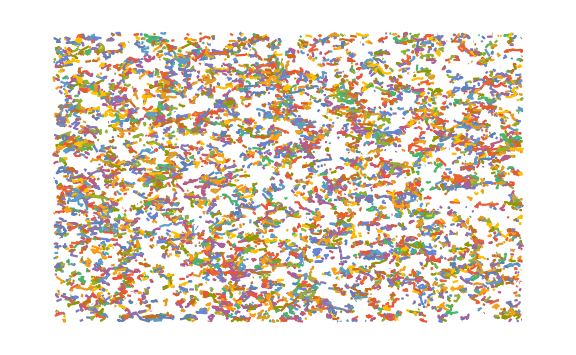

```mathematica
ListPlot[Table[traj[i],{i,Max@Keys@traj}],Joined->True,PlotRange->Full,ImageSize->Large,Axes->False]
```

#### subpixel

```mathematica
(track2=SMTrack["C:\\Users\\aliha\\Downloads\\images-SPT\\nmeth.tif","subpixelLocalize"->True]);//AbsoluteTiming
```

{185.605,Null}

```mathematica
traj2=Replace[Table[seeds[i],{i,Max@Keys@seeds}],x:Except[{__List}]:> {x},1];
```

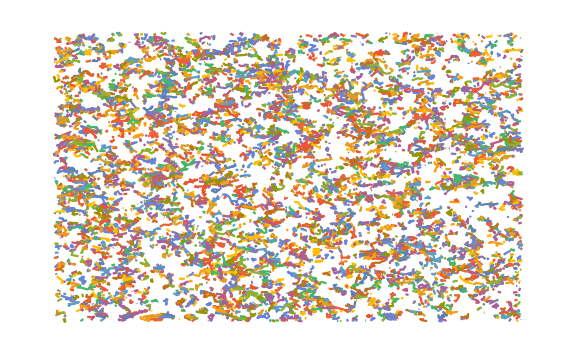

```mathematica
ListPlot[traj2,Joined->True,PlotRange->Full,ImageSize->Large,Axes->False]
```

#### misc

```mathematica
funcGenerator["subpixelLocalize"-> True]
```

```mathematica
DownValues@detectParticle
```

{HoldPattern[detectParticle[image_Image,LoGkernel_:2,thresh_:0.75]]:>Block[{segImage,masks,boundingboxes,shapes},segImage=segmentImage[image,LoGkernel,thresh];{masks,shapes,boundingboxes}=Transpose[Values[ComponentMeasurements[segImage,{Mask,Shape,BoundingBox}]]];MapThread[modelFit[image,##1]&,{masks,shapes,boundingboxes}]]}

```mathematica
Length@images
```

100

```mathematica
(det =ParallelTable[Quiet@detectParticle[i],{i,images}]);//AbsoluteTiming
```

{123.715,Null}

```mathematica
If[True,
currentKeyVector = Range@*Length@det[[1]];
seeds=<|Thread[ currentKeyVector ->Partition[ det[[1]],1] ]|>
];
```

```mathematica
Fold[stackCorrespondence[##,True,"subpixelLocalize"-> True]&,First@det,Rest@det];//AbsoluteTiming
```

{61.2138,Null}

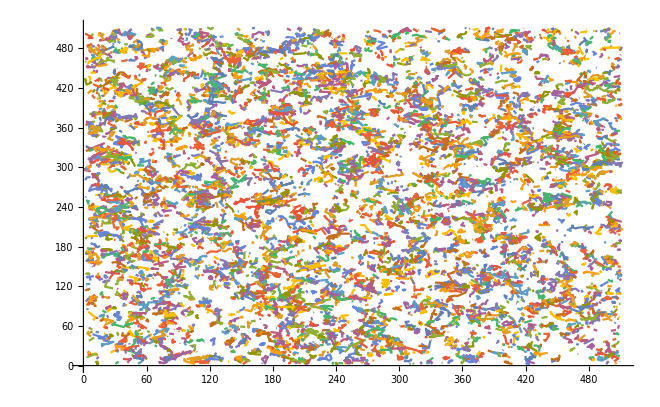

```mathematica
ListPlot[
Replace[Table[seeds[i],{i,Max@Keys@seeds}],x:Except[{__List}]:> {x},1],Joined->True]
```